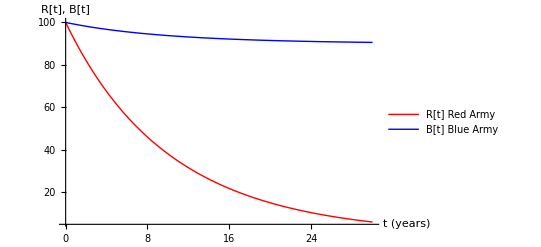

```mathematica
(*Define the parameters*)c1=0.001;
c2=0.0001;
R0=100;
B0=100;

(*Define the differential equations*)
eqn1=R'[t]==-c1*R[t]*B[t];
eqn2=B'[t]==-c2*R[t]*B[t];

(*Solve the system of differential equations with initial conditions*)
sol=NDSolve[{eqn1,eqn2,R[0]==R0,B[0]==B0},{R,B},{t,0,30}];

(*Plot the solutions*)
Plot[Evaluate[{R[t],B[t]}/.sol[[1]]],{t,0,30},PlotRange->All,PlotStyle->{Red,Blue},PlotLegends->{"R[t] Red Army","B[t] Blue Army"},AxesLabel->{"t (years)","R[t], B[t]"},AxesStyle->Arrowheads[0.03]]
```

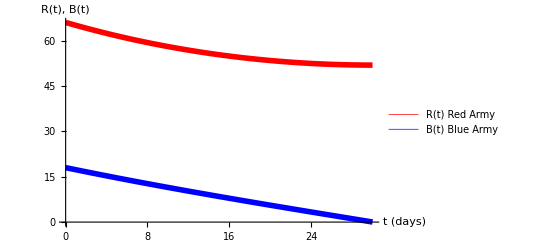

```mathematica
a1=0.0544;
a2=0.0106;

eqn1=R'[t]==-a1*B[t];
eqn2=B'[t]==-a2*R[t];

sol=NDSolve[{eqn1,eqn2,R[0]==66,B[0]==18},{R,B},{t,0,30}];

Plot[Evaluate[{R[t],B[t]}/.sol],{t,0,30},PlotRange->All,PlotStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.01]}},PlotLegends->{"R(t) Red Army","B(t) Blue Army"},AxesLabel->{"t (days)","R(t), B(t)"},AxesStyle->Arrowheads[{0,0.03}]]
```